```mathematica
n=3;
phenotypelist=Tuples[{0,1},n];
phenotypelist1=Reverse@Select[phenotypelist,Count[#,1]==1&];
```

```mathematica
alpha=Table[10,n];
r=Table[1,n+1];
d=Table[1*10^-6,n];
y=Table[10^-5,n];
S0=20000;
mout0=Join[{S0},Table[0,n]];
X0=Table[10^-4,n];
p=0.01;
```

```mathematica
Ig3list={1,3.16,5,10,25,31.6,50,100};
```

```mathematica
(*cond1:0<rb<ra<1*)
ralist=Table[i,{i,0.15,0.9,0.15}];
d1=d[[1]]/y[[1]];
Ig3list={2.5};
Bigset={};
Do[
rblist=Table[i,{i,(ralist[[j]]/50),ralist[[j]]-(ralist[[j]]/50),ralist[[j]]/50}];
paraset={};
Igc3list=Rationalize@Table[{Ig3list[[k]],(ralist[[j]])*(d1/ralist[[j]])/Ig3list[[k]]},{k,Length@Ig3list}];
Do[
Ig1=(d1*rblist[[i]]-ralist[[j]]*(d1/ralist[[j]])* ralist[[j]]* rblist[[i]])/(ralist[[j]]*(d1/ralist[[j]])*ralist[[j]]-d1 rblist[[i]]);
c1=-(d1*ralist[[j]]*(d1/ralist[[j]])(-1+ rblist[[i]]))/((d1-ralist[[j]]*(d1/ralist[[j]])*ralist[[j]])  rblist[[i]]);
paraset=Join[paraset,{{Ig1,c1}}];
,{i,Length@rblist}];
(*paraset=Select[paraset,#[[1]]>0&&#[[2]]>0&];*)
Parasets=Partition[Flatten[Table[{paraset[[k1]],paraset[[k2]]},{k1,1,Length@paraset},{k2,1,Length@paraset}]],4];
bigsets=Table[Join[Parasets[[j]],Igc3list[[i]]],{i,Length@Igc3list},{j,Length@Parasets}];
Bigset=Join[Bigset,bigsets];
,{j,1,6}];
Length@Bigset
```

```mathematica
label=Flatten[Table[{ralist[[i]],Ig3list[[j]]},{i,Length@ralist},{j,Length@Igc3list}],1]
```

```mathematica
Do[
list={};
list1={};
Parasets1=Bigset[[j]];
Do[
set=Parasets1[[i]];
Ig=Take[set,{1,-2,2}];
Ct=Take[set,{2,-1,2}];
test=Table[(Ig[[i]]*Ct[[-1]]*Ig[[-1]])/((Ig[[i]]*Ct[[i]])-Ct[[-1]]*Ig[[-1]]),{i,1,Length@Ig-1}];
mout=Table[ToExpression["mout"<>ToString@j],{j,1,n+1}];
V=Table[ToExpression["V"<>ToString@i],{i,1,n}];
min=Table[ToExpression["min"<>ToString@i<>ToString@j],{i,1,n},{j,1,n+1}];
vs=Flatten@Table[phenotypelist1[[i,j]]*alpha[[j]],{i,1,n},{j,1,1}];
vi=Table[phenotypelist1[[i,j]]*alpha[[j]]*min[[i,j]][t],{i,1,n},{j,2,n}];
vp=Table[Ig[[i]]*min[[i,n+1]][t],{i,1,n}];
v0=Table[0,{i,1,n}];
v=Transpose@Join[{v0},{vs},Transpose@vi,{vp}];
g=Table[y[[i]]*(vp[[i]]*Ct[[i]]),{i,1,n}];
var=Flatten@Join[mout,min,V];
mineqn={};
Veqn={};
Do[
mouteqn={};
Do[eqn1={min[[i,j]]'[t]==v[[i,j]]-v[[i,j+1]]+r[[j]]*(mout[[j]][t]-min[[i,j]][t])};
eqn2=If[j==1,{mout[[j]]'[t]==0},
{mout[[j]]'[t]==-Sum[V[[i]][t]*r[[j]]*(mout[[j]][t]-min[[i,j]][t]),{i,1,n}]}];
mineqn=Join[mineqn,eqn1];
mouteqn=Join[mouteqn,eqn2];
,{j,1,n+1}];
eqn3={V[[i]]'[t]==g[[i]]*V[[i]][t]*(1-Sum[V[[i]][t],{i,1,n}]/p)-d[[i]]*V[[i]][t]};
Veqn=Join[Veqn,eqn3];
,{i,1,n}];
NDeqn=Flatten@Join[mineqn,mouteqn,Veqn];
mineqn0={};
Veqn0={};
Do[
mouteqn0={};
Do[eqn01={min[[i,j]][0]==0};
eqn02={mout[[j]][0]==mout0[[j]]};
mineqn0=Join[mineqn0,eqn01];
mouteqn0=Join[mouteqn0,eqn02];
,{j,1,n+1}];
eqn30={V[[i]][0]==X0[[i]]};
Veqn0=Join[Veqn0,eqn30];
,{i,1,n}];
NDeqn0=Flatten@Join[mineqn0,mouteqn0,Veqn0];
eqn=Join[NDeqn,NDeqn0];
result=NDSolve[eqn,var,{t,0,110000000}];
moutv=First@Evaluate[Table[mout[[i]][100000000],{i,1,n+1}]/.result];
minv=Flatten@First@Evaluate[Table[min[[i,j]][100000000],{i,1,n},{j,1,n+1}]/.result];
xb=First@Evaluate[Table[V[[i]][100000000],{i,1,n}]/.result];
total=Total@xb;
xratio=Round[xb/total,0.0001];
list1=Join[list1,{Join[test,xratio,{total}]}];
list=Join[list,{Join[moutv,minv,xb,{total}]}];
If[Divisible[i,2400]==True,Print[j]];
,{i,1,Length@Parasets1}];
Export[FileNameJoin[{NotebookDirectory[],"cond1","Results-ra="<>ToString[label[[j,1]]]<>"-Ig3="<>ToString[label[[j,2]]]<>".txt"}],list];
Export[FileNameJoin[{NotebookDirectory[],"cond1","PlotResults-ra="<>ToString[label[[j,1]]]<>"-Ig3="<>ToString[label[[j,2]]]<>".xlsx"}],list1];
,{j,1,Length@Bigset}];
```

```mathematica
Ig3list={1,2.5,3.16,5,10,25,31.6,50,100};
label=Flatten[Table[{ralist[[i]],Ig3list[[j]]},{i,Length@ralist},{j,Length@Ig3list}],1]
```

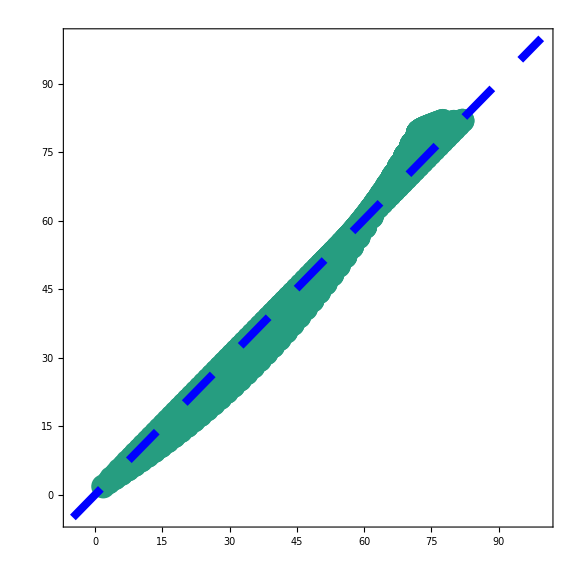

{3.4018,0.997002,1.00521}

```mathematica
Gridplot1={};
Gridplot2={};
Gridplot3={};
hlist={};
numlist={};
Do[data=Flatten@Import[FileNameJoin[{NotebookDirectory[],"cond1","PlotResults-ra="<>ToString[label[[j,1]]]<>"-Ig3="<>ToString[label[[j,2]]]<>".xlsx"}]];
data=Partition[data,6];
data1=Select[data,#[[-1]]>0.0001&];
num=Length@data1;
numlist=Join[numlist,{num}];

plotdata2=Table[{data1[[i,1]],data1[[i,2]],data1[[i,-2]]*100},{i,Length@data1}];
desplot=ListDensityPlot[plotdata2,ColorFunction->"BlueGreenYellow",PlotRange->{{0,1},{0,1},{-1,100}},LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,42],ImageSize->Large,VertexColors->Table[ColorData["BlueGreenYellow"][Rescale[plotdata2[[i,3]],{0,100},{0,1}]],{i,1,Length@plotdata2}],InterpolationOrder->1.0,Mesh->100];
fit=h/.FindFit[plotdata2,100*((x1^h+x2^h)/2)^(1/h),h,{x1,x2}];
theplot=Plot3D[100*((x^fit+y^fit)/2)^(1/fit),{x,0,1},{y,0,1},BoxRatios->{1, 1, 1},ImageSize->Large,PlotRange->{{0,1},{0,1},{0,105}},Boxed->True,BoxStyle->Directive[Thickness[0.005],Black,Bold,36],PlotStyle->Directive[Opacity[0.5],RGBColor[{199/255,237/255,233/255}]],LabelStyle->Directive[Black,Bold,30],AxesStyle->Directive[Thickness[0.005],Black]];
speedplot2=ListPointPlot3D[plotdata2,ImageSize->Large,BoxRatios->{1, 1, 1},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.01]],PlotRange->{{0,1},{0,1},{0,105}},Boxed->True,BoxStyle->Directive[Thickness[0.005],Black,Bold,36],LabelStyle->Directive[Black,Bold,30],AxesStyle->Directive[Thickness[0.005],Black]];
plot2=Show[theplot,speedplot2];
hlist=Join[hlist,{fit}];
Gridplot1=Join[Gridplot1,{desplot}];
Gridplot2=Join[Gridplot2,{plot2}];

predictvalue=Table[100*((plotdata2[[i,1]]^fit+plotdata2[[i,2]]^fit)/(n-1))^(1/fit),{i,Length@plotdata2}];
plotdata=Transpose@Join[{predictvalue},{Flatten@Take[plotdata2,All,{-1}]}];
linearfit=LinearModelFit[plotdata,x,x,IncludeConstantBasis->False];

linearfit["BestFitParameters"];
paralist={fit,linearfit["AdjustedRSquared"],First@linearfit["BestFitParameters"]};

plot=Show[ListPlot[plotdata,AspectRatio->1,PlotRange->{{-5,100},{-5,100}},ImageSize->Large,PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PlotRange->{{-1.5,3.5},{-50,2000}},PointSize[0.03]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],Plot[linearfit[x],{x,-5,100},AspectRatio->1,PlotRange->{{-5,100},{-5,100}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.01],Dashing[0.05]],PlotRange->{{-1.5,3.25},{-50,2000}},Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]];

plotdata4=SortBy[Table[{data1[[i,1]],data1[[i,2]],Log[5,data1[[i,3]]/(data1[[i,4]])]},{i,Length@data1}],Last];
desplot1=ListDensityPlot[plotdata4,ColorFunction->"BlueGreenYellow",PlotRange->{{0,1},{0,1},{-1.4,1.4}},LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,42],ImageSize->Large,InterpolationOrder->1.0,Mesh->All,VertexColors->Table[ColorData["BlueGreenYellow"][Rescale[plotdata4[[i,3]],{-1.4,1.4},{0,1}]],{i,1,Length@plotdata4}]];
Gridplot3=Join[Gridplot3,{desplot1}];
,{j,46,46}];
plot
paralist
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","3-member-example.tif"}],plot];
```

```mathematica
Gridplot1new1=Partition[Gridplot1,9];
grid21=Flatten@Take[Gridplot1new1,All,{1}];
grid22=Flatten@Take[Gridplot1new1,All,{4}];
grid23=Flatten@Take[Gridplot1new1,All,{5}];
grid24=Flatten@Take[Gridplot1new1,All,{6}];
grid25=Flatten@Take[Gridplot1new1,All,{8}];
outputgrid1=Grid[Transpose@Join[{grid21},{grid22},{grid23},{grid24},{grid25}]];
Export[FileNameJoin[{NotebookDirectory[],"plot","Gridplot1.tif"}],outputgrid1];
```

```mathematica
Gridplot2new1=Partition[Gridplot2,9];
grid21=Flatten@Take[Gridplot2new1,All,{1}];
grid22=Flatten@Take[Gridplot2new1,All,{4}];
grid23=Flatten@Take[Gridplot2new1,All,{5}];
grid24=Flatten@Take[Gridplot2new1,All,{6}];
grid25=Flatten@Take[Gridplot2new1,All,{8}];
outputgrid2=Grid[Transpose@Join[{grid21},{grid22},{grid23},{grid24},{grid25}]];
Export[FileNameJoin[{NotebookDirectory[],"plot","Gridplot2.tif"}],outputgrid2];
```

```mathematica
Gridplot3new1=Partition[Gridplot3,9];
grid21=Flatten@Take[Gridplot3new1,All,{1}];
grid22=Flatten@Take[Gridplot3new1,All,{4}];
grid23=Flatten@Take[Gridplot3new1,All,{5}];
grid24=Flatten@Take[Gridplot3new1,All,{6}];
grid25=Flatten@Take[Gridplot3new1,All,{8}];
outputgrid3=Grid[Transpose@Join[{grid21},{grid22},{grid23},{grid24},{grid25}]];
Export[FileNameJoin[{NotebookDirectory[],"plot","Gridplot3.tif"}],outputgrid3];
```

```mathematica
logIg3=N@Table[Table[Log10[Ig3list[[i]]],{i,1,Length@Ig3list}],Length@ralist]
hlist2=Partition[Transpose@Join[{Flatten@logIg3},{hlist}],Length@Ig3list]
```

```mathematica
hplot={};
Do[
hplot1=Show[ListLinePlot[{Select[N@hlist2[[i]],#[[2]]≠0&]},AspectRatio->1,PlotRange->{{-0.2,2.2},{0,3.5}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.03],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],ListPlot[Select[N@hlist2[[i]],#[[2]]≠0&],AspectRatio->1,ImageSize->Large,PlotRange->{{-0.2,2.2},{0,3.5}},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.07]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]];
hplot=Join[hplot,{{hplot1}}];
,{i,1,6}];
hplot1=Grid[hplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","hplot.tif"}],hplot1];
```

```mathematica
numlist
```

```mathematica
numlist1=100*numlist/2401;
numlist2=Partition[Transpose@Join[{Flatten@logIg3},{numlist1}],Length@Ig3list];
numplot={};
Do[
numplot1=Show[ListLinePlot[{SortBy[N@numlist2[[i]],First]},AspectRatio->1,PlotRange->{{-0.2,2.2},{0,105}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.03],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],ListPlot[numlist2[[i]],AspectRatio->1,ImageSize->Large,PlotRange->{{-0.2,2.2},{0,105}},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.07]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]];
numplot=Join[numplot,{{numplot1}}];
,{i,1,6}];
numplot1=Grid[numplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","numplot.tif"}],numplot1];
```

```mathematica
Ig3list={1,3.16,10,31.6,100};
label=Flatten[Table[{ralist[[i]],Ig3list[[j]]},{i,Length@ralist},{j,Length@Ig3list}],1];
indexlist={};
boxlist={};
Do[data=Flatten@Import[FileNameJoin[{NotebookDirectory[],"cond1","PlotResults-ra="<>ToString[label[[j,1]]]<>"-Ig3="<>ToString[label[[j,2]]]<>".xlsx"}]];
data=Partition[data,6];
data1=Select[data,#[[-1]]>0.0001&];
plotdata4=SortBy[Table[{data1[[i,1]],data1[[i,2]],data1[[i,3]]/(data1[[i,4]])},{i,Length@data1}],Last];
index=First[MaximalBy[plotdata4,Last]][[3]]-First[MinimalBy[plotdata4,Last]][[3]];
indexlist=Join[indexlist,{index}];
boxplotdata=If[data1=={},Table[0,100],Flatten@Take[plotdata4,All,{-1}]];
boxlist=Join[boxlist,{boxplotdata}];
,{j,1,Length@label}];
```

```mathematica
boxlist2=Partition[boxlist,Length@Ig3list];
boxplot={};
Do[
boxplot1=BoxWhiskerChart[boxlist2[[i]],{"Notched",{"MedianMarker",0.5,Black},{"Whiskers", Thick}, {"Fences", Thick}},Method->{"BoxRange"->(Quantile[#,{0,1/1000,1/2,999/1000,1},{{1,-1},{0,1}}]&)},ImageSize->Large,PlotRange->{{0.6,5.4},{0.9985,1.0015}},ChartStyle->Directive[RGBColor[{38/255,157/255,128/255}],EdgeForm[{Black,Thick}]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,36],AspectRatio->1/1,Axes->False];
boxplot=Join[boxplot,{boxplot1}];
,{i,1,6}];
boxplot2=Grid[Partition[boxplot,1],Spacings->{1,3.5}];
Export[FileNameJoin[{NotebookDirectory[],"plot","boxplot.tif"}],boxplot2];
```

```mathematica
Length@boxlist2
```

```mathematica
indexlist=indexlist;
indexlist1=Partition[Transpose@Join[{Flatten@logIg3},{indexlist}],Length@Ig3list];
indexplot={};
Do[
indexplot1=Show[ListLinePlot[{SortBy[N@indexlist1[[i]],First]},AspectRatio->1,PlotRange->{{-0.2,2.2},{-0.0001,0.0021}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.03],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],ListPlot[indexlist1[[i]],AspectRatio->1,ImageSize->Large,PlotRange->{{-0.2,2.2},{-0.001,0.001}},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.07]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]];
indexplot=Join[indexplot,{{indexplot1}}];
,{i,1,6}];
indexplot1=Grid[indexplot];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","indexplot.tif"}],indexplot1];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","hlist.xlsx"}],hlist];
Export[FileNameJoin[{NotebookDirectory[],"plot","numlist.xlsx"}],numlist];
Export[FileNameJoin[{NotebookDirectory[],"plot","indexlist.xlsx"}],indexlist];
```